```mathematica
(*determinación de Q*)
datafrecond1={{0,Log[1.151067715]},{1.0848825,Log[1.129547402]},{2.169765,Log[1.125339542]},{3.2546475,Log[1.11882716]},{4.33953,Log[1.110005359]},{5.4244125,Log[1.102326289]},{6.509295,Log[1.094670089]},{7.5941775,Log[1.087608761]},{8.67906,Log[1.079833184]},{9.7639425,Log[1.072564539]},{10.848825,Log[1.065314819]},{11.9337075, Log[1.058316911]},{13.01859,Log[1.050876939]},{14.1034725,Log[1.044442844]},{15.188355,Log[1.037121808]},{16.2732375,Log[1.03070799]}};
```

```mathematica
datafit1=NonlinearModelFit[datafrecond1,{t*a+b},{a,b},t]
```

FittedModel[0.133083-0.00640336 t]

```mathematica
datafit1[{"BestFit","ParameterTable"}]
```

{0.133083-0.00640336 t, | Estimate | Standard Error | t-Statistic | P-Value
a | -0.00640336 | 0.000122613 | -52.2244 | 1.90199×10^-17
b | 0.133083 | 0.00117103 | 113.646 | 3.65729×10^-22}

```mathematica
pplot1=ListPlot[datafrecond1 ,PlotStyle->{Black,Thickness[0.003]},PlotLegends-> {"Datos experimentales"}];
graph1=Plot[datafit1[t],{t,-0.1,17},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{-0.1,17},{0.02,0.15}},Frame->True,FrameLabel->{Style["t / s",Bold,16],Style["ln(v / m s⁻.b9)",16,Bold]}];

Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
dataerr1=ErrorListPlot[{{{0,Log[1.151067715]}, ErrorBar[0,0.001724595]},{{1.0848825,Log[1.129547402]},ErrorBar[3.96246*10^(-5),0.001724578]},{{2.169765,Log[1.125339542]},ErrorBar[7.92493*10^(-5),0.001724575]},{{3.2546475,Log[1.11882716]},ErrorBar[0.000118874,0.00172457]},{{4.33953,Log[1.110005359]},ErrorBar[0.000158499,0.001724563]},{{5.4244125,Log[1.102326289]},ErrorBar[0.000198123,0.001724557]},{{6.509295,Log[1.094670089]},ErrorBar[0.000237748,0.001724551]},{{7.5941775,Log[1.087608761]},ErrorBar[0.000277372,0.001724546]},{{8.67906,Log[1.079833184]},ErrorBar[0.000316997,0.00172454]},{{9.7639425,Log[1.072564539]},ErrorBar[0.000356622,0.001724535]},{{10.848825,Log[1.065314819]},ErrorBar[0.000396246,0.001724529]},{{11.9337075, Log[1.058316911]},ErrorBar[0.000435871,0.001724524]},{{13.01859,Log[1.050876939]},ErrorBar[0.000475496,0.001724519]},{{14.1034725,Log[1.044442844]},ErrorBar[0.00051512,0.001724514]},{{15.188355,Log[1.037121808]},ErrorBar[0.000554745,0.001724509]},{{16.2732375,Log[1.03070799]},ErrorBar[0.000594369,0.001724504]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

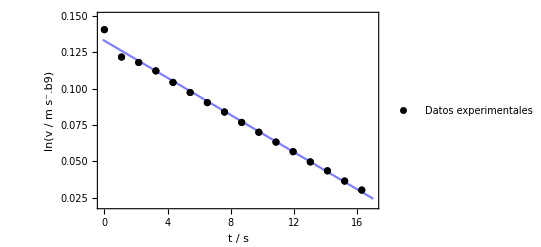

```mathematica
Show[graph1,pplot1,dataerr1]
```

```mathematica
(*determinación de I*)
datafrecond2={{9.80665,29.8116},{9.769332736,29.9209},{9.657664951,29.5936},{9.472496504,29.0521},{9.21523664,28.1961},{8.88784326,27.1441},{8.492808026,25.6036},{8.033137395,24.1081},{7.512329738,22.5625},{6.934348716,20.7025},{6.303593113,18.5761},{5.62486336,16.5649},{4.903325,14.2884}};

datafit2=NonlinearModelFit[datafrecond2,{g*a+b},{a,b},g]
```

FittedModel[-1.6403+3.22566 g]

```mathematica
datafit2[{"BestFit","ParameterTable"}]
```

{-1.6403+3.22566 g, | Estimate | Standard Error | t-Statistic | P-Value
a | 3.22566 | 0.0213877 | 150.819 | 1.36448×10^-19
b | -1.6403 | 0.175479 | -9.34756 | 1.44464×10^-6}

```mathematica
pplot2=ListPlot[datafrecond2 ,PlotStyle->{Black,Thickness[0.003]},PlotLegends-> {"Datos experimentales"}];
graph2=Plot[datafit2[g],{g,4.5,10},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{4.7,10},{13,31}},Frame->True,FrameLabel->{Style["gₑ / m s⁻.b2",Bold,16],Style["ωₒ.b2 / rad.b2 s⁻.b2",16,Bold]}];

Needs["ErrorBarPlots`"];
```

```mathematica
dataerr2=ErrorListPlot[{{{9.80665,29.8116}, ErrorBar[0,0.024024]},{{9.769332736,29.9209},ErrorBar[0.001491743,0.01094]},{{9.657664951,29.5936},ErrorBar[0.002972133,0.0022848]},{{9.472496504,29.0521},ErrorBar[0.004429904,0.0023716]},{{9.21523664,28.1961},ErrorBar[0.00585396,0.0070092]},{{8.88784326,27.1441},ErrorBar[0.007233464,0.004689]},{{8.492808026,25.6036},ErrorBar[0.008557917,0.0037444]},{{8.033137395,24.1081},ErrorBar[0.009817239,0.0033388]},{{7.512329738,22.5625},ErrorBar[0.011001845,0.00304]},{{6.934348716,20.7025},ErrorBar[0.012102722,0.002821]},{{6.303593113,18.5761},ErrorBar[0.013111489,0.0031032]},{{5.62486336,16.5649},ErrorBar[0.01402047,0.0027676]},{{4.903325,14.2884},ErrorBar[0.014822746,0.0031752]}}AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

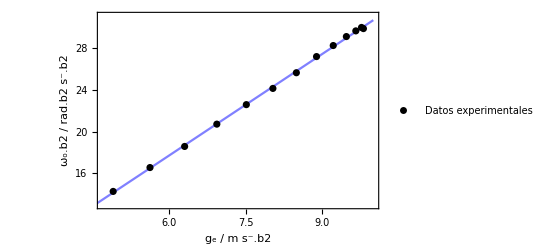

```mathematica
Show[graph2,pplot2,dataerr2]
```

```mathematica
(*Cálculo v0 y tau*)
```

```mathematica
v0=E^(0.13308348474422863)
```

1.14235

```mathematica
errv0=v0*0.0011710317271807547
```

0.00133772

```mathematica
τ=1/(2*0.006403363928602255)
```

78.084

```mathematica
errτ=0.00012261260140726573/(2*0.006403363928602255^2)
```

1.49516

```mathematica
Q[T_,τ_]:=((2*Pi)/T)*τ;
```

```mathematica
Q[2.16977,78.0839579906778]
```

226.114

```mathematica
errQ=Sqrt[((2*Pi/2.16977)*1.495163686487911)^2+((2*Pi/2.16977^2)*0.00004)^2]
```

4.32967